James Gardner
Working from Yap thesis, 2020
Deriving eq. 7.12 from eq. 7.8 and eq. 7.17 from 7.16.

Watch out, Yap thesis uses X_2=-i(a+a†) which gives a different sign in the 2nd and 4th rows of Γ

```mathematica
(*I is reserved for ⅈ, be careful not to confuse I and Id!*)
Id=IdentityMatrix[4];
(*eq. 7.6*)
M=κa({{-1, 0, 0, x ⅇ^(ⅈ θb)}, {0, -1, x ⅇ^(-ⅈ θb), 0}, {0, x ⅇ^(ⅈ θb), -1, 0}, {x ⅇ^(-ⅈ θb), 0, 0, -1}});
(*eq 7.11*)
Γ=({{1, 1, 0, 0}, {-ⅈ, ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, -ⅈ, ⅈ}});
Xfin=({{Xfins1}, {Xfins2}, {Xfini1}, {Xfini2}});
Xlin=({{Xlins1}, {Xlins2}, {Xlini1}, {Xlini2}});
```

```mathematica
(*eqs. 7.9, 7.10*)
T =FullSimplify[2κaf Γ.Inverse[ⅈ ω Id-M].Inverse[Γ]-Id];
Tl = FullSimplify[2(κaf κal)^(1/2)Γ. Inverse[ⅈ ω Id-M].Inverse[Γ]];
```

```mathematica
Xfout=FullSimplify[T.Xfin+Tl.Xlin];
Xfout//MatrixForm
```

(-(2 Xlins1 √(κaf κal) (κa+ⅈ ω)+Xfins1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)+2 x κa ((Xfini1 κaf+Xlini1 √(κaf κal)) Cos[θb]+(Xfini2 κaf+Xlini2 √(κaf κal)) Sin[θb]))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlins2 √(κaf κal) (κa+ⅈ ω)+Xfins2 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)-2 x κa (Xfini2 κaf+Xlini2 √(κaf κal)) Cos[θb]+2 x κa (Xfini1 κaf+Xlini1 √(κaf κal)) Sin[θb])/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlini1 √(κaf κal) (κa+ⅈ ω)+Xfini1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)+2 x κa ((Xfins1 κaf+Xlins1 √(κaf κal)) Cos[θb]+(Xfins2 κaf+Xlins2 √(κaf κal)) Sin[θb]))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)
-(2 Xlini2 √(κaf κal) (κa+ⅈ ω)+Xfini2 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2)-2 x κa (Xfins2 κaf+Xlins2 √(κaf κal)) Cos[θb]+2 x κa (Xfins1 κaf+Xlins1 √(κaf κal)) Sin[θb])/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2))

```mathematica
Collect[Xfout[[1]][[1]]/.{θb->0},{Xlins1,Xlins2,Xlini1,Xlini2,Xfins1,Xfins2,Xfini1,Xfini2}]
```

-(2 x Xfini1 κa κaf)/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(2 x Xlini1 κa √(κaf κal))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(2 Xlins1 √(κaf κal) (κa+ⅈ ω))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)-(Xfins1 (κa ((-1+x^2) κa+2 κaf)-2 ⅈ (κa-κaf) ω+ω^2))/((-1+x^2) κa^2-2 ⅈ κa ω+ω^2)

```mathematica
(*the variance of Xfouts1: if assuming all inputs are vacuum, then just sum the abs sq of the co-efficients of each input fluctuation.*)
Vout=FullSimplify[(1/(((-1+x^2) κa^2+ω^2)^2+(-2  κa ω)^2))((-2 x κa κaf)^2+ (-2 x κa √(κaf κal))^2+(-2 κa √(κaf κal))^2+(-2 √(κaf κal)ω)^2+(κa ((-1+x^2) κa+2 κaf)+ω^2)^2+(-2 (κa-κaf) ω)^2)/.{κal->κa-κaf}]
```

1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)

```mathematica
(*for reference, the desired value is (7.12, 7.18)*)
Goal=Simplify[1+(8 x^2(κaf/κa))/(x^4+2 x^2((ω/κa)^2-1)+((ω/κa)^2+1)^2)];
Goal==Vout
```

True

```mathematica
(*Attempting to recover 7.17, the covariance matrix*)
Assumps = {x>0,κa>0,κaf>0,κal>0,θb>0,ω>0,κa≥κaf};
V = FullSimplify[(T.ConjugateTranspose[T]+Tl.ConjugateTranspose[Tl])/.{θb->0,κal->κa-κaf},Assumptions->Assumps];
V//MatrixForm
```

(1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | (4 x κa κaf ((1+x^2) κa^2+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0
0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | -(4 x κa κaf ((1+x^2) κa^2+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)
(4 x κa κaf ((1+x^2) κa^2+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0
0 | -(4 x κa κaf ((1+x^2) κa^2+ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4))

```mathematica
V[[1]][[1]]
```

1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 ω^2+ω^4)

```mathematica
(*the diagonal elements of the covariance matrix are the output variances*)
V[[1]][[1]] == Vout==Goal
```

True

Repeating calculation using other convention for Γ

```mathematica
Γsgn=({{1, 1, 0, 0}, {ⅈ, -ⅈ, 0, 0}, {0, 0, 1, 1}, {0, 0, ⅈ, -ⅈ}});
Tfsgn =FullSimplify[2κaf Γsgn.Inverse[ⅈ Ω Id-M].Inverse[Γsgn]-Id];
Tlsgn = FullSimplify[2(κaf κal)^(1/2)Γsgn. Inverse[ⅈ Ω Id-M].Inverse[Γsgn]];
Vsgn=FullSimplify[(Tfsgn.Tfsgn†+Tlsgn.Tlsgn†)/.{θb->0,κal->κa-κaf},Assumptions->{x>0,κaf>0,Ω>0,κa≥κaf}];
Vsgn//MatrixForm
(V/.{ω->Ω})==Vsgn
```

(1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | (4 x κa κaf ((1+x^2) κa^2+Ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0
0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | -(4 x κa κaf ((1+x^2) κa^2+Ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4)
(4 x κa κaf ((1+x^2) κa^2+Ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0
0 | -(4 x κa κaf ((1+x^2) κa^2+Ω^2))/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4) | 0 | 1+(8 x^2 κa^3 κaf)/((-1+x^2)^2 κa^4+2 (1+x^2) κa^2 Ω^2+Ω^4))

True

```mathematica
SetDirectory[NotebookDirectory[]];
(*print the notebook to a .pdf, the notebook needs to be saved for this to function*)
NotebookPrint[EvaluationNotebook[],NotebookDirectory[]<>"NOPO_matrices.pdf"]
```

Plotting the (co)variances from degenerate and nondegenerate OPO’s against frequency

```mathematica
(*above: eq3.5 from Min Jet's thesis, the κ formula is only an approximation?*)
```

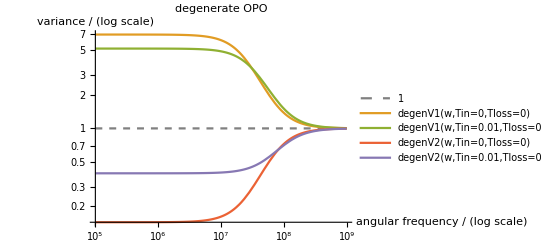

```mathematica
(*degenerate OPO, using values from Sheon Chua's thesis*)
c=3 10^8(*m s^-1*);
L =1(*m*);
tRoundTrip=(2L)/c(*=1/FSR*); (*assumes linear cavity, unclear if factor of 2 req*)
Tout=0.1;
kout=Tout^(1/2)/tRoundTrip;
x=0.45;
degenV1[w_,Tin_,Tloss_]:=(
kin=Tin^(1/2)/tRoundTrip;
kloss=Tloss^(1/2)/tRoundTrip;
ktot=kout+kin+kloss;
g=x ktot;
1+(4 kout g)/(w^2+(g-ktot)^2))
degenV2[w_,Tin_,Tloss_]:=(
kin=Tin^(1/2)/tRoundTrip;
kloss=Tloss^(1/2)/tRoundTrip;
ktot=kout+kin+kloss;
g=x ktot;
1-(4 kout g)/(w^2+(g+ktot)^2))
(*(*λ=1μm=10^-6 m, want to consider sidebands of carrier, so look at frequencies around w=2π c/λ*)
(*because of rotating frame, aren't all frequencies already relative to ω/2?*)
lambda=10^-6(*m*);
wCarrier=N[2π c/lambda];(*~1.9*10^15 Hz*)*)
LogLogPlot[{1,degenV1[w,Tin=0,Tloss=0],degenV1[w,Tin=0.01,Tloss=0.001],degenV2[w,Tin=0,Tloss=0],degenV2[w,Tin=0.01,Tloss=0.001]},{w,10^5,10^9},AxesLabel->{"angular frequency / (log scale)", "variance / (log scale)"},PlotLegends->"Expressions",PlotLabel->"degenerate OPO",PlotStyle->{{Dashed,Gray},,,,}]
```

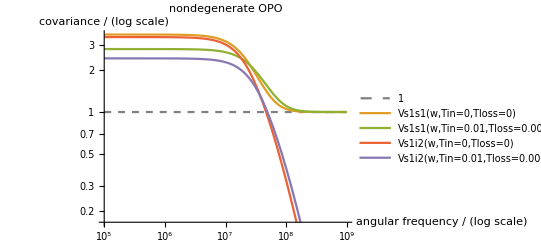

```mathematica
(*nondegenerate OPO, from above calculation: V[[1]][[1]], V[[1]][[3]]*)
Vs1s1[w_,Tin_,Tloss_]:=(
kin=Tin^(1/2)/tRoundTrip;
kloss=Tloss^(1/2)/tRoundTrip;
ktot=kout+kin+kloss;
g=x ktot;
1+(8 x^2 ktot^3 kout)/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
Vs1i2[w_,Tin_,Tloss_]:=(
kin=Tin^(1/2)/tRoundTrip;
kloss=Tloss^(1/2)/tRoundTrip;
ktot=kout+kin+kloss;
g=x ktot;
(4 x ktot kout ((1+x^2) ktot^2+w^2))/((-1+x^2)^2 ktot^4+2 (1+x^2) ktot^2 w^2+w^4))
LogLogPlot[{1,Vs1s1[w,Tin=0,Tloss=0],Vs1s1[w,Tin=0.01,Tloss=0.001],Vs1i2[w,Tin=0,Tloss=0],Vs1i2[w,Tin=0.01,Tloss=0.001]},{w,10^5,10^9},AxesLabel->{"angular frequency / (log scale)", "covariance / (log scale)"},PlotLegends->"Expressions",PlotLabel->"nondegenerate OPO",PlotStyle->{{Dashed,Gray},,,,}]
```